0.845621

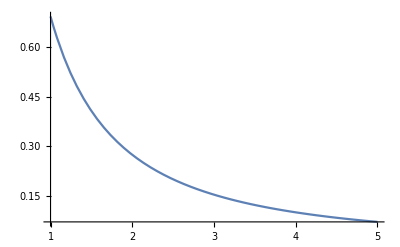

```mathematica
g=Log[x+1]/x^2;
A=Integrate[g,{x,1,5}];
A//N
Plot[g,{x,1,5}]
```

```mathematica
k=1/A;
f=k*g;
Integrate[f,{x,1,5}]
```

1

```mathematica
EV=Integrate[x f,{x,1,5}];
EV//N
```

2.27858

```mathematica
Var=Integrate[(x-EV)^2 f,{x,1,5}];
Var//N
```

1.15167

Find the probability that 2<x<3.5

```mathematica
Integrate[f,{x,2,3.5}]
```

0.323692

```mathematica
g=9-x^2
A=Integrate[g,{x,0,3}]
```

9-x^2

18

```mathematica
k=1/A
f=k*g
```

1/18

1/18 (9-x^2)

```mathematica
Integrate[f,{x,0,1}]
%//N
```

13/27

0.481481

```mathematica
Integrate[f,{x,0,2}]
%//N
```

23/27

0.851852

```mathematica
Integrate[f,{x,1,2}]
%//N
```

10/27

0.37037

```mathematica
Integrate[f,{x,0,x}]
%//N
```

x/2-x^3/54

0.5 x-0.0185185 x^3

```mathematica
EV=Integrate[x f,{x,0,3}]
%//N
```

9/8

1.125

```mathematica
Var=Integrate[(x-EV)^2 f,{x,0,3}]
%//N
```

171/320

0.534375